```mathematica
(*s=InputString["Enter xml file name","tooth.xml"]//StringReplace[#," "->""]&;*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive.xml"];*)
xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_strong_red.xml"];
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_weak_red.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_green_1000.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_red_1000.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"vorts1.xml"];*)
{tfifile,volumefile,legends,face,imagefilenames,txtfilenames,{featurefilename,visibilityfilename},resultxml,imagefile,rawfile,dataname,plotpath,imagepath}=xml;
(*Column[xml,Background->{{Lighter@LightYellow,Lighter@LightBlue}},Frame->True,FrameStyle->Directive[LightGray,Thin,Dashed]]*)

tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;

d = Import[volumefile,"Image3D"];
colorized=Image3D[d,ColorFunction->rgbafunction];
{lightness,chroma,hue,opacity}=ImageApply[List@@rgbafunction[#]&,d]//Image3D[#,ColorSpace->"RGB"]&//ColorSeparate[ColorConvert[#,"LCH"]]&;
(*lo=ImageMultiply[lightness,opacity];
co=ImageMultiply[chroma,opacity];*)
(*g1=ImageDifference[GaussianFilter[lightness,{2,Sqrt[2]/8.*2}],GaussianFilter[lightness,{4,Sqrt[2]/8.*4}]]
g2=ImageDifference[GaussianFilter[chroma,{2,Sqrt[2]/8.*2}],GaussianFilter[chroma,{4,Sqrt[2]/8.*4}]]
g3=ImageDifference[GaussianFilter[hue,{2,Sqrt[2]/8.*2}],GaussianFilter[hue,{4,Sqrt[2]/8.*4}]];
g4=ImageDifference[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]];*)
{g1,g2}=ParallelMap[ImageDifference[GaussianFilter[#,{2,Sqrt[2]/8.*2}],GaussianFilter[#,{4,Sqrt[2]/8.*4}]]&,{lightness,chroma}];

pos=intensity[[#]]&/@Flatten@Position[alpha,_?(#==0&)];
index=Flatten@Position[alpha,_?(#>0&)];
features=Table[ImageApply[If[#≥pos[[i]] && #≤pos[[i+1]],1,0]&,d],{i,1,Length[pos],2}];
chartcolors=rgbcolors[[#]]&/@index;
colorizedfeatures=ImageMultiply[colorized,#]&/@features;
viewpoints=<|"top":>Top,"back":>Back,"left":>Left,"bottom":>Bottom,"front":>Front,"right":>Right|>;
MapIndexed[Export[StringReplace[imagefile,"."->"_"<>ToString[First[#2]]<>"."],Show[#,Boxed->False,ViewPoint->viewpoints[face]]]&,colorizedfeatures];

intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
(*fun=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];*)
(*Plot[fun[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
index0=Flatten@Position[alpha0,_?(#>0&)];

(* nucleon 0.1 0.3 0.6 vortex 0.4 0.3 0.3 *)
targets=<|2->{0.2,0.8},3->{0.1,0.3,0.6},4->{0.1,0.2,0.3,0.4}|>;
target=targets[Length[index0]]
CloseKernels[];
LaunchKernels[8];
Clear[f];
Clear[data];
records={};
epsilon=0.01;
stepsize=0.05;
iterationcount1=50;
iterationcount2=15;
```

{0.1,0.3,0.6}

```mathematica
top:=Module[{list,count,img,list2,list3,d1},(* top *)
list=Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d1=Image3D[list3]]
back:=Module[{list,count,img,list2,list3,tmp,d2},(* back *)
list=Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left:=Module[{list,count,img,list2,list3,tmp,d3},(* left *)
list=Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom:=Module[{list,count,img,list2,list3,d4},(* bottom *)
list=Reverse@Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d4=Image3D[Reverse[list3]]]
front:=Module[{list,count,img,list2,list3,tmp,d5},(* front *)
list=Reverse@Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right:=Module[{list,count,img,list2,list3,tmp,d6},(* right *)
list=Reverse@Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices=<|"top":>top,"back":>back,"left":>left,"bottom":>bottom,"front":>front,"right":>right|>;
```

```mathematica
top2:=Module[{list,img,list2,list3,df,d1},(* top *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d1=Image3D[list3]
]
back2:=Module[{list,img,list2,list3,tmp,df,d2},(* back *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left2:=Module[{list,img,list2,list3,tmp,df,d3},(* left *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom2:=Module[{list,img,list2,list3,df,d4},(* bottom *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d4=Image3D[Reverse[list3]]]
front2:=Module[{list,img,list2,list3,tmp,df,d5},(* front *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right2:=Module[{list,img,list2,list3,tmp,df,d6},(* right *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices2=<|"top":>top2,"back":>back2,"left":>left2,"bottom":>bottom2,"front":>front2,"right":>right2|>;
```

```mathematica
VisibilitySaliency[peaks_]:=Module[{alpha2,fun,vis,viss,vs,mean,total},
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
Visibility[fun_]:=Module[{vis,viss,vs,mean,total},
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
```

```mathematica
(* x(k+1)=x(k)-(f-f0)/(f'-f0') *)
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
iteration=0;
previous={0,{0,0,0},{0,0,0}};
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,gradient,direction,square},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
gradient:=2*(mean-target);
square:=(mean-target)^2;
steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,g0,s0,dy,dx},
{rms0,mean0,p0,g0,s0}=previous;
dy=square-s0;
dx=gradient-g0;
If[Product[i,{i,dx}]≠0,direction=Normalize[dy/dx]*Norm[gradient];-direction*stepsize,-gradient*stepsize]
]];
previous={rms,mean,peaks,gradient,square};
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps,gradient,direction}
],{iterator,iterationcount1}];
```

2.85338

37

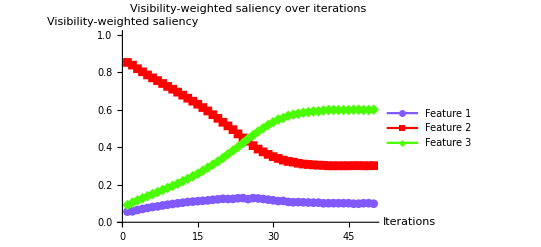

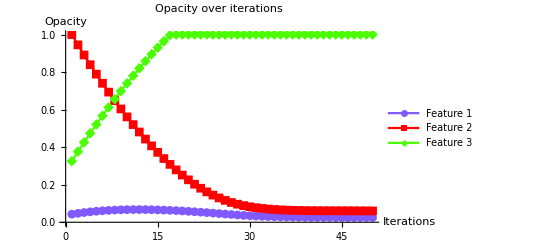

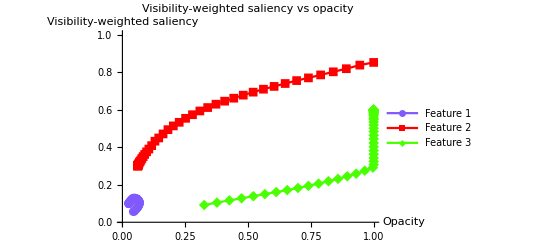

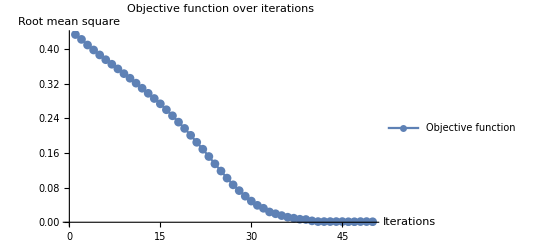

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps |  | 
1 | 0.0566538
0.851543
0.0918031 | 0.0431373
1.
0.32549 | 0.433721 | 0.00433462
-0.0551543
0.0508197 | -0.0866924
1.10309
-1.01639 | direction$2029607
2 | 0.0581638
0.837143
0.104693 | 0.0474719
0.944846
0.37631 | 0.422533 | 0.00420347
-0.053723
0.0495196 | -0.0836723
1.07429
-0.990614 | -0.0840693
1.07446
-0.990391
3 | 0.0654655
0.817979
0.116555 | 0.0516753
0.891123
0.425829 | 0.409558 | 0.00375904
-0.0519342
0.0481752 | -0.0690689
1.03596
-0.96689 | -0.0751808
1.03868
-0.963504
4 | 0.0708195
0.801464
0.127717 | 0.0554344
0.839188
0.474005 | 0.398066 | 0.00314044
-0.0502472
0.0471068 | -0.0583611
1.00293
-0.944567 | -0.0628088
1.00494
-0.942135
5 | 0.0762921
0.784912
0.138796 | 0.0585748
0.788941
0.521111 | 0.386614 | 0.00260585
-0.0485995
0.0459936 | -0.0474159
0.969825
-0.922409 | -0.0521171
0.97199
-0.919873
6 | 0.0811103
0.769149
0.149741 | 0.0611807
0.740342
0.567105 | 0.375584 | 0.00209908
-0.0470131
0.044914 | -0.0377794
0.938298
-0.900518 | -0.0419815
0.940262
-0.898281
7 | 0.0845135
0.754703
0.160783 | 0.0632798
0.693329
0.612019 | 0.365106 | 0.0016945
-0.0455393
0.0438448 | -0.0309729
0.909407
-0.878434 | -0.03389
0.910786
-0.876896
8 | 0.0894032
0.739207
0.17139 | 0.0649742
0.647789
0.655864 | 0.354364 | 0.0012847
-0.0440287
0.042744 | -0.0211935
0.878414
-0.85722 | -0.0256941
0.880573
-0.854879
9 | 0.0936482
0.72369
0.182662 | 0.066259
0.603761
0.698608 | 0.343378 | 0.000834091
-0.0424658
0.0416317 | -0.0127036
0.84738
-0.834676 | -0.0166818
0.849317
-0.832635
10 | 0.0973133
0.708894
0.193793 | 0.067093
0.561295
0.74024 | 0.332769 | 0.000444838
-0.0409763
0.0405315 | -0.00537343
0.817788
-0.812415 | -0.00889676
0.819527
-0.81063
11 | 0.100971
0.693131
0.205899 | 0.0675379
0.520319
0.780771 | 0.321387 | 0.0000843083
-0.0394038
0.0393195 | 0.00194141
0.786262
-0.788203 | -0.00168617
0.788076
-0.78639
12 | 0.104258
0.67711
0.218631 | 0.0676222
0.480915
0.820091 | 0.309662 | -0.000256598
-0.0377968
0.0380534 | 0.00851676
0.75422
-0.762737 | 0.00513197
0.755936
-0.761068
13 | 0.107802
0.660936
0.231262 | 0.0673656
0.443118
0.858144 | 0.297939 | -0.000591366
-0.0361907
0.0367821 | 0.015603
0.721873
-0.737476 | 0.0118273
0.723814
-0.735641
14 | 0.110038
0.645056
0.244906 | 0.0667742
0.406927
0.894926 | 0.285923 | -0.000873603
-0.0345733
0.0354469 | 0.0200752
0.690112
-0.710188 | 0.0174721
0.691466
-0.708938
15 | 0.112308
0.628817
0.258875 | 0.0659006
0.372354
0.930373 | 0.273641 | -0.00109277
-0.0329543
0.0340471 | 0.0246161
0.657634
-0.682251 | 0.0218553
0.659087
-0.680942
16 | 0.114171
0.611059
0.27477 | 0.0648079
0.3394
0.96442 | 0.259957 | -0.00129002
-0.0311735
0.0324635 | 0.0283425
0.622118
-0.65046 | 0.0258004
0.62347
-0.64927
17 | 0.116402
0.592802
0.290797 | 0.0635178
0.308226
0.996884 | 0.246041 | -0.00148662
-0.0293629
0.0308495 | 0.0328032
0.585603
-0.618406 | 0.0297323
0.587258
-0.616991
18 | 0.11983
0.572907
0.307263 | 0.0620312
0.278863
1. | 0.231348 | -0.00175584
-0.0274155
0.0291714 | 0.0396591
0.545814
-0.585473 | 0.0351169
0.548311
-0.583427
19 | 0.122167
0.553764
0.324069 | 0.0602754
0.251448
1. | 0.216815 | -0.00203176
-0.02548
0.0275118 | 0.0443336
0.507529
-0.551863 | 0.0406351
0.509601
-0.550236
20 | 0.125105
0.53249
0.342405 | 0.0582436
0.225968
1. | 0.200862 | -0.00227341
-0.0233849
0.0256583 | 0.0502107
0.46498
-0.51519 | 0.0454682
0.467698
-0.513166
21 | 0.123984
0.513331
0.362685 | 0.0559702
0.202583
1. | 0.184756 | -0.00235197
-0.02136
0.023712 | 0.0479686
0.426662
-0.474631 | 0.0470393
0.4272
-0.47424
22 | 0.124558
0.49332
0.382123 | 0.0536182
0.181223
1. | 0.168766 | -0.00231735
-0.0194132
0.0217306 | 0.0491152
0.386639
-0.435754 | 0.0463471
0.388264
-0.434611
23 | 0.127899
0.4705
0.401601 | 0.0513009
0.161809
1. | 0.151889 | -0.002485
-0.0172351
0.0197201 | 0.0557973
0.341001
-0.396798 | 0.0496999
0.344703
-0.394403
24 | 0.128634
0.449103
0.422263 | 0.0488159
0.144574
1. | 0.134959 | -0.00265993
-0.0150378
0.0176977 | 0.0572677
0.298206
-0.355473 | 0.0531986
0.300756
-0.353954
25 | 0.12322
0.431917
0.444863 | 0.046156
0.129537
1. | 0.118334 | -0.00242255
-0.013129
0.0155515 | 0.0464396
0.263834
-0.310274 | 0.0484509
0.262579
-0.31103
26 | 0.128589
0.408117
0.463294 | 0.0437334
0.116408
1. | 0.101973 | -0.00239916
-0.0111154
0.0135146 | 0.0571787
0.216234
-0.273412 | 0.0479832
0.222308
-0.270291
27 | 0.126692
0.389986
0.483322 | 0.0413343
0.105292
1. | 0.0864558 | -0.00253661
-0.00908995
0.0116266 | 0.0533849
0.179972
-0.233357 | 0.0507321
0.181799
-0.232531
28 | 0.12402
0.375047
0.500933 | 0.0387977
0.0962022
1. | 0.0730826 | -0.00232315
-0.00756014
0.00988329 | 0.0480406
0.150093
-0.198134 | 0.046463
0.151203
-0.197666
29 | 0.120252
0.36152
0.518229 | 0.0364745
0.0886421
1. | 0.0602255 | -0.00200011
-0.00616977
0.00816988 | 0.0405034
0.123039
-0.163543 | 0.0400023
0.123395
-0.163398
30 | 0.116873
0.349672
0.533455 | 0.0344744
0.0824723
1. | 0.0489224 | -0.00166402
-0.00498386
0.00664788 | 0.0337462
0.0993435
-0.13309 | 0.0332804
0.0996771
-0.132958
31 | 0.112952
0.340083
0.546965 | 0.0328104
0.0774885
1. | 0.0391028 | -0.00132492
-0.00398715
0.00531207 | 0.0259043
0.0801655
-0.10607 | 0.0264984
0.079743
-0.106241
32 | 0.113578
0.330967
0.555454 | 0.0314855
0.0735013
1. | 0.0322885 | -0.00120054
-0.00321513
0.00441567 | 0.0271565
0.0619346
-0.0890911 | 0.0240109
0.0643026
-0.0883134
33 | 0.108238
0.324102
0.56766 | 0.0302849
0.0702862
1. | 0.0237674 | -0.000925315
-0.00233576
0.00326108 | 0.0164754
0.0482047
-0.0646801 | 0.0185063
0.0467152
-0.0652215
34 | 0.10629
0.3203
0.57341 | 0.0293596
0.0679504
1. | 0.0196529 | -0.000657597
-0.00200984
0.00266744 | 0.0125806
0.0406002
-0.0531808 | 0.0131519
0.0401968
-0.0533487
35 | 0.10731
0.314118
0.578572 | 0.028702
0.0659406
1. | 0.0154047 | -0.00059856
-0.0015148
0.00211336 | 0.0146196
0.0282364
-0.042856 | 0.0119712
0.0302959
-0.0422671
36 | 0.106278
0.310042
0.58368 | 0.0281034
0.0644258
1. | 0.0116421 | -0.000585049
-0.00104028
0.00162533 | 0.012556
0.0200847
-0.0326407 | 0.011701
0.0208056
-0.0325066
37 | 0.105271
0.307924
0.586805 | 0.0275184
0.0633855
1. | 0.00939319 | -0.000515727
-0.000802324
0.00131805 | 0.0105418
0.0158488
-0.0263907 | 0.0103145
0.0160465
-0.026361
38 | 0.104417
0.305398
0.590186 | 0.0270027
0.0625832
1. | 0.00695126 | -0.000412183
-0.000566811
0.000978994 | 0.00883348
0.010795
-0.0196285 | 0.00824366
0.0113362
-0.0195799
39 | 0.104608
0.304341
0.591051 | 0.0265905
0.0620164
1. | 0.00632866 | -0.000430363
-0.000464429
0.000894792 | 0.00921518
0.00868233
-0.0178975 | 0.00860725
0.00928858
-0.0178958
40 | 0.100955
0.303381
0.595664 | 0.0261601
0.061552
1. | 0.00322214 | -0.000189952
-0.000263732
0.000453684 | 0.00190919
0.00676288
-0.00867207 | 0.00379905
0.00527464
-0.00907369
41 | 0.101356
0.300778
0.597866 | 0.0259702
0.0612882
1. | 0.00152738 | -0.0000761236
-0.000137002
0.000213126 | 0.00271274
0.00155536
-0.0042681 | 0.00152247
0.00274004
-0.00426251
42 | 0.101356
0.300778
0.597866 | 0.025894
0.0611512
1. | 0.00152738 | -0.000135637
-0.0000777678
0.000213405 | 0.00271274
0.00155536
-0.0042681 | direction$2048343
43 | 0.101356
0.300778
0.597866 | 0.0257584
0.0610735
1. | 0.00152738 | -0.000135637
-0.0000777678
0.000213405 | 0.00271274
0.00155536
-0.0042681 | direction$2048800
44 | 0.101356
0.300778
0.597866 | 0.0256228
0.0609957
1. | 0.00152738 | -0.000135637
-0.0000777678
0.000213405 | 0.00271274
0.00155536
-0.0042681 | direction$2049257
45 | 0.101356
0.300778
0.597866 | 0.0254871
0.0609179
1. | 0.00152738 | -0.000135637
-0.0000777678
0.000213405 | 0.00271274
0.00155536
-0.0042681 | direction$2049714
46 | 0.0988185
0.301546
0.599635 | 0.0253515
0.0608402
1. | 0.00114306 | -0.0000101326
-0.000134654
0.000144786 | -0.002363
0.00309243
-0.000729429 | 0.000202652
0.00269308
-0.00289573
47 | 0.0988185
0.301546
0.599635 | 0.0253414
0.0607055
1. | 0.00114306 | 0.00011815
-0.000154621
0.0000364715 | -0.002363
0.00309243
-0.000729429 | direction$2050628
48 | 0.101356
0.300778
0.597866 | 0.0254595
0.0605509
1. | 0.00152738 | -0.0000135394
-0.000179928
0.000193467 | 0.00271274
0.00155536
-0.0042681 | 0.000270789
0.00359856
-0.00386935
49 | 0.101356
0.300778
0.597866 | 0.025446
0.060371
1. | 0.00152738 | -0.000135637
-0.0000777678
0.000213405 | 0.00271274
0.00155536
-0.0042681 | direction$2051542
50 | 0.0988185
0.301546
0.599635 | 0.0253103
0.0602932
1. | 0.00114306 | -0.0000101326
-0.000134654
0.000144786 | -0.002363
0.00309243
-0.000729429 | 0.000202652
0.00269308
-0.00289573

```mathematica
t2-t1
iteration
saliency5=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_newton.png",saliency5];
opacity5=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_newton.png",opacity5];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity5=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_newton.png",saliencyopacity5];
rmslist5=#3&@@@list;
rms5=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_newton.png",rms5];
table5=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_newton.png",table5];
path5=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path5]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,gradient},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
gradient=2*(mean-target);
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps,gradient}
],{iterator,iterationcount1}];
```

2.845624

37

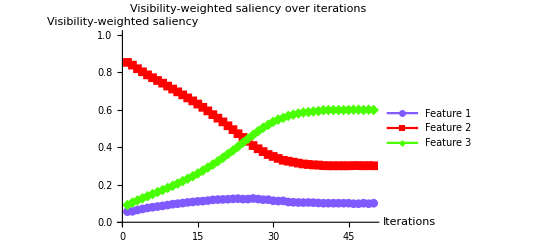

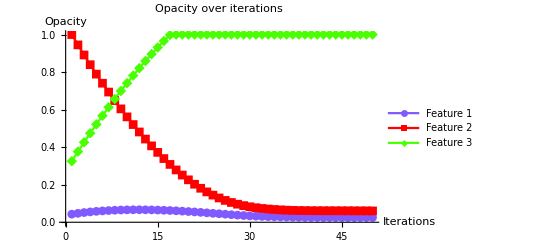

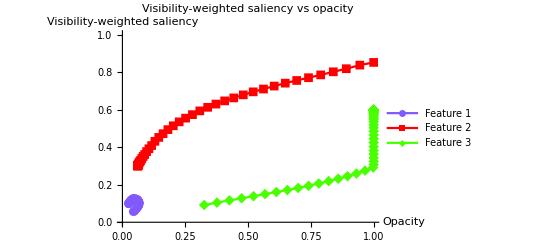

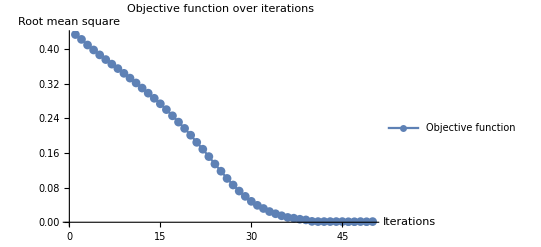

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | 
1 | 0.0566538
0.851543
0.0918031 | 0.0431373
1.
0.32549 | 0.433721 | 0.00433462
-0.0551543
0.0508197 | -0.0866924
1.10309
-1.01639
2 | 0.0581638
0.837143
0.104693 | 0.0474719
0.944846
0.37631 | 0.422533 | 0.00418362
-0.0537143
0.0495307 | -0.0836723
1.07429
-0.990614
3 | 0.0654655
0.817979
0.116555 | 0.0516555
0.891131
0.425841 | 0.409558 | 0.00345345
-0.0517979
0.0483445 | -0.0690689
1.03596
-0.96689
4 | 0.0708222
0.80149
0.127688 | 0.0551089
0.839333
0.474185 | 0.398088 | 0.00291778
-0.050149
0.0472312 | -0.0583556
1.00298
-0.944624
5 | 0.0762826
0.785044
0.138673 | 0.0580267
0.789184
0.521416 | 0.386718 | 0.00237174
-0.0485044
0.0461327 | -0.0474349
0.970088
-0.922653
6 | 0.0799996
0.77006
0.14994 | 0.0603985
0.74068
0.567549 | 0.375903 | 0.00200004
-0.047006
0.045006 | -0.0400008
0.94012
-0.900119
7 | 0.0837749
0.755361
0.160864 | 0.0623985
0.693674
0.612555 | 0.365357 | 0.00162251
-0.0455361
0.0439136 | -0.0324502
0.910721
-0.878271
8 | 0.0871895
0.741114
0.171697 | 0.064021
0.648138
0.656468 | 0.355053 | 0.00128105
-0.0441114
0.0428303 | -0.025621
0.882227
-0.856606
9 | 0.0916192
0.725596
0.182784 | 0.0653021
0.604027
0.699299 | 0.344128 | 0.000838084
-0.0425596
0.0417216 | -0.0167617
0.851193
-0.834431
10 | 0.0961713
0.709785
0.194044 | 0.0661401
0.561467
0.74102 | 0.333036 | 0.000382872
-0.0409785
0.0405956 | -0.00765743
0.81957
-0.811913
11 | 0.0989591
0.694723
0.206318 | 0.066523
0.520488
0.781616 | 0.321866 | 0.000104088
-0.0394723
0.0393682 | -0.00208175
0.789446
-0.787364
12 | 0.102156
0.678634
0.219211 | 0.0666271
0.481016
0.820984 | 0.310037 | -0.000215571
-0.0378634
0.0380789 | 0.00431142
0.757267
-0.761579
13 | 0.105694
0.662417
0.231888 | 0.0664115
0.443153
0.859063 | 0.298264 | -0.000569442
-0.0362417
0.0368112 | 0.0113888
0.724834
-0.736223
14 | 0.10825
0.646587
0.245163 | 0.0658421
0.406911
0.895874 | 0.286414 | -0.000825003
-0.0346587
0.0354837 | 0.0165001
0.693173
-0.709674
15 | 0.111029
0.629578
0.259393 | 0.0650171
0.372252
0.931358 | 0.273713 | -0.00110294
-0.0329578
0.0340607 | 0.0220588
0.659156
-0.681215
16 | 0.112599
0.612288
0.275113 | 0.0639141
0.339295
0.965419 | 0.260278 | -0.00125989
-0.0312288
0.0324887 | 0.0251977
0.624576
-0.649773
17 | 0.115403
0.593264
0.291332 | 0.0626543
0.308066
0.997907 | 0.245979 | -0.00154034
-0.0293264
0.0308668 | 0.0308068
0.586529
-0.617335
18 | 0.119169
0.57335
0.307482 | 0.0611139
0.278739
1. | 0.231412 | -0.00191686
-0.027335
0.0292518 | 0.0383372
0.546699
-0.585036
19 | 0.120713
0.554617
0.32467 | 0.0591971
0.251404
1. | 0.216845 | -0.0020713
-0.0254617
0.027533 | 0.0414261
0.509234
-0.55066
20 | 0.121703
0.534789
0.343507 | 0.0571258
0.225943
1. | 0.201151 | -0.00217035
-0.0234789
0.0256493 | 0.043407
0.469579
-0.512986
21 | 0.122797
0.513904
0.363299 | 0.0549554
0.202464
1. | 0.184664 | -0.00227972
-0.0213904
0.0236701 | 0.0455944
0.427808
-0.473403
22 | 0.124558
0.49332
0.382123 | 0.0526757
0.181073
1. | 0.168766 | -0.00245576
-0.019332
0.0217877 | 0.0491152
0.386639
-0.435754
23 | 0.125629
0.471666
0.402705 | 0.0502199
0.161741
1. | 0.151714 | -0.00256289
-0.0171666
0.0197295 | 0.0512578
0.343332
-0.39459
24 | 0.123313
0.451925
0.424762 | 0.047657
0.144575
1. | 0.134577 | -0.00233134
-0.0151925
0.0175238 | 0.0466268
0.30385
-0.350476
25 | 0.123347
0.431359
0.445295 | 0.0453257
0.129382
1. | 0.117946 | -0.00233465
-0.0131359
0.0154705 | 0.046693
0.262718
-0.309411
26 | 0.126664
0.408499
0.464837 | 0.0429911
0.116247
1. | 0.101245 | -0.00266642
-0.0108499
0.0135163 | 0.0533284
0.216997
-0.270326
27 | 0.123628
0.391589
0.484783 | 0.0403246
0.105397
1. | 0.0860656 | -0.00236277
-0.00915894
0.0115217 | 0.0472555
0.183179
-0.230434
28 | 0.120228
0.376422
0.503349 | 0.0379619
0.0962377
1. | 0.07209 | -0.00202284
-0.00764222
0.00966506 | 0.0404568
0.152844
-0.193301
29 | 0.120385
0.360899
0.518716 | 0.035939
0.0885955
1. | 0.0598087 | -0.00203845
-0.00608991
0.00812836 | 0.040769
0.121798
-0.162567
30 | 0.114544
0.350542
0.534913 | 0.0339006
0.0825056
1. | 0.0483128 | -0.00145444
-0.00505425
0.00650869 | 0.0290888
0.101085
-0.130174
31 | 0.112952
0.340083
0.546965 | 0.0324461
0.0774513
1. | 0.0391028 | -0.00129522
-0.00400827
0.00530349 | 0.0259043
0.0801655
-0.10607
32 | 0.113707
0.330202
0.556091 | 0.0311509
0.073443
1. | 0.0317706 | -0.00137072
-0.00302023
0.00439095 | 0.0274145
0.0604045
-0.087819
33 | 0.107998
0.325453
0.56655 | 0.0297802
0.0704228
1. | 0.024703 | -0.000799768
-0.00254526
0.00334503 | 0.0159954
0.0509052
-0.0669005
34 | 0.10629
0.3203
0.57341 | 0.0289804
0.0678776
1. | 0.0196529 | -0.000629029
-0.00203001
0.00265904 | 0.0125806
0.0406002
-0.0531808
35 | 0.105409
0.315047
0.579544 | 0.0283514
0.0658476
1. | 0.0149903 | -0.000540862
-0.00150474
0.0020456 | 0.0108172
0.0300948
-0.040912
36 | 0.104814
0.310572
0.584614 | 0.0278105
0.0643428
1. | 0.0111303 | -0.000481419
-0.00105715
0.00153857 | 0.00962838
0.021143
-0.0307714
37 | 0.105271
0.307924
0.586805 | 0.0273291
0.0632857
1. | 0.00939319 | -0.000527091
-0.000792442
0.00131953 | 0.0105418
0.0158488
-0.0263907
38 | 0.104417
0.305398
0.590186 | 0.026802
0.0624932
1. | 0.00695126 | -0.000441674
-0.00053975
0.000981424 | 0.00883348
0.010795
-0.0196285
39 | 0.102761
0.304817
0.592422 | 0.0263603
0.0619535
1. | 0.00542411 | -0.000276145
-0.000481704
0.000757848 | 0.0055229
0.00963407
-0.015157
40 | 0.101244
0.301616
0.59714 | 0.0260842
0.0614718
1. | 0.00202794 | -0.000124388
-0.000161601
0.000285988 | 0.00248775
0.00323201
-0.00571977
41 | 0.101356
0.300778
0.597866 | 0.0259598
0.0613102
1. | 0.00152738 | -0.000135637
-0.0000777678
0.000213405 | 0.00271274
0.00155536
-0.0042681
42 | 0.101356
0.300778
0.597866 | 0.0258242
0.0612324
1. | 0.00152738 | -0.000135637
-0.0000777678
0.000213405 | 0.00271274
0.00155536
-0.0042681
43 | 0.101356
0.300778
0.597866 | 0.0256885
0.0611546
1. | 0.00152738 | -0.000135637
-0.0000777678
0.000213405 | 0.00271274
0.00155536
-0.0042681
44 | 0.101356
0.300778
0.597866 | 0.0255529
0.0610769
1. | 0.00152738 | -0.000135637
-0.0000777678
0.000213405 | 0.00271274
0.00155536
-0.0042681
45 | 0.101356
0.300778
0.597866 | 0.0254173
0.0609991
1. | 0.00152738 | -0.000135637
-0.0000777678
0.000213405 | 0.00271274
0.00155536
-0.0042681
46 | 0.0988185
0.301546
0.599635 | 0.0252816
0.0609213
1. | 0.00114306 | 0.00011815
-0.000154621
0.0000364715 | -0.002363
0.00309243
-0.000729429
47 | 0.0988185
0.301546
0.599635 | 0.0253998
0.0607667
1. | 0.00114306 | 0.00011815
-0.000154621
0.0000364715 | -0.002363
0.00309243
-0.000729429
48 | 0.101356
0.300778
0.597866 | 0.0255179
0.0606121
1. | 0.00152738 | -0.000135637
-0.0000777678
0.000213405 | 0.00271274
0.00155536
-0.0042681
49 | 0.0988185
0.301546
0.599635 | 0.0253823
0.0605343
1. | 0.00114306 | 0.00011815
-0.000154621
0.0000364715 | -0.002363
0.00309243
-0.000729429
50 | 0.101356
0.300778
0.597866 | 0.0255004
0.0603797
1. | 0.00152738 | -0.000135637
-0.0000777678
0.000213405 | 0.00271274
0.00155536
-0.0042681

```mathematica
t2-t1
iteration
saliency1=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_fixed.png",saliency1];
opacity1=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_fixed.png",opacity1];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity1=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_fixed.png",saliencyopacity1];
rmslist1=#3&@@@list;
rms1=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_fixed.png",rms1];
table1=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_fixed.png",table1];
path1=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path1]}];
```

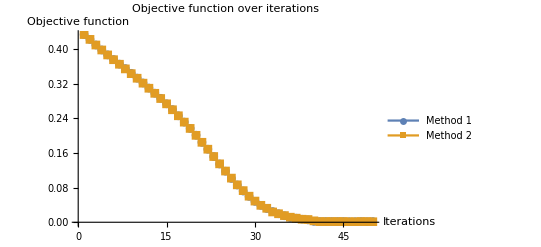

```mathematica
rmslists1=ListLinePlot[{rmslist1,rmslist5},PlotLegends->{"Method 1","Method 2"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Objective function"}]
Export[plotpath<>dataname<>"_rms_fixed_newton.png",rmslists1];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*parallel gradient*)
multipliers={1,2,4,8};
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,meanlist,peaklist,rmslist,minindex},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=ParallelMap[Clip[peaks+steps*#,{0,1}]&,multipliers];
meanlist=ParallelMap[VisibilitySaliency[#]&,peaklist];
rmslist=ParallelMap[RootMeanSquare[#-target]&,meanlist];
minindex=First@Ordering[rmslist,1];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=meanlist[[minindex]];
If[t2==0 && rmslist[[minindex]]<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,iterationcount2}];
```

1.778634

4

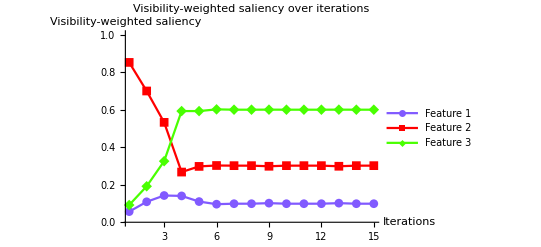

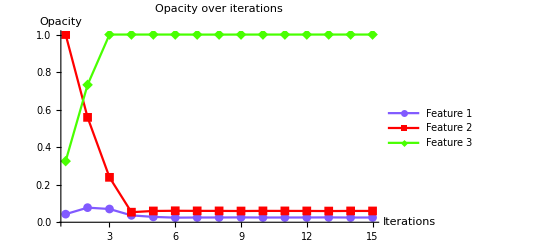

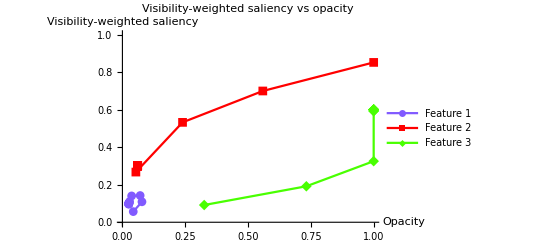

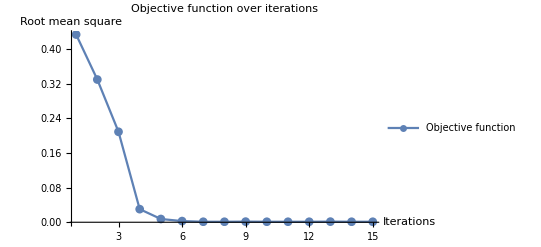

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.0566538
0.851543
0.0918031 | 0.0431373
1.
0.32549 | 0.433721 | 0.00433462
-0.0551543
0.0508197 | 8
2 | 0.109027
0.699312
0.191661 | 0.0778142
0.558766
0.732048 | 0.329784 | -0.000902684
-0.0399312
0.0408339 | 8
3 | 0.14244
0.532156
0.325404 | 0.0705927
0.239316
1. | 0.209046 | -0.00424397
-0.0232156
0.0274596 | 8
4 | 0.1403
0.267363
0.592337 | 0.0366409
0.053591
1. | 0.0302658 | -0.00403004
0.00326374
0.000766303 | 2
5 | 0.11017
0.297563
0.592268 | 0.0285809
0.0601185
1. | 0.00750894 | -0.00101697
0.000243727
0.00077324 | 4
6 | 0.0962455
0.302352
0.601402 | 0.024513
0.0610934
1. | 0.00268296 | 0.000375446
-0.000235199
-0.000140248 | 2
7 | 0.0988119
0.301527
0.599661 | 0.0252639
0.060623
0.99972 | 0.00113426 | 0.000118811
-0.000152739
0.0000339274 | 1
8 | 0.0988119
0.301527
0.599661 | 0.0253827
0.0604703
0.999753 | 0.00113426 | 0.000118811
-0.000152739
0.0000339274 | 4
9 | 0.101768
0.298279
0.599953 | 0.0258579
0.0598593
0.999889 | 0.00142497 | -0.000176815
0.000172137
4.67825×10^-6 | 4
10 | 0.0988185
0.301546
0.599635 | 0.0251507
0.0605479
0.999908 | 0.00114306 | 0.00011815
-0.000154621
0.0000364715 | 1
11 | 0.0988185
0.301546
0.599635 | 0.0252688
0.0603932
0.999944 | 0.00114306 | 0.00011815
-0.000154621
0.0000364715 | 1
12 | 0.0988185
0.301546
0.599635 | 0.025387
0.0602386
0.999981 | 0.00114306 | 0.00011815
-0.000154621
0.0000364715 | 4
13 | 0.101768
0.298279
0.599953 | 0.0258596
0.0596201
1. | 0.00142497 | -0.000176815
0.000172137
4.67825×10^-6 | 4
14 | 0.0988185
0.301546
0.599635 | 0.0251523
0.0603087
1. | 0.00114306 | 0.00011815
-0.000154621
0.0000364715 | 1
15 | 0.0988185
0.301546
0.599635 | 0.0252705
0.0601541
1. | 0.00114306 | 0.00011815
-0.000154621
0.0000364715 | 1

```mathematica
t2-t1
iteration
saliency2=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_parallelsearch.png",saliency2];
opacity2=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_parallelsearch.png",opacity2];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity2=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_parallelsearch.png",saliencyopacity2];
rmslist2=#3&@@@list;
rms2=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_parallelsearch.png",rms2];
table2=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_parallelsearch.png",table2];
path2=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path2]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*line search*)
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaklist,minindex,minrms,minmean,rms2,mean2},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=Map[Clip[peaks+steps*#,{0,1}]&,multipliers];
minindex=1;
minmean=VisibilitySaliency[peaklist[[minindex]]];
minrms=RootMeanSquare[minmean-target];
Do[mean2=VisibilitySaliency[peaklist[[i]]];
rms2=RootMeanSquare[mean2-target];
If[rms2<minrms,minrms=rms2;minmean=mean2;minindex=i,Return[i]];
,{i,Range[2,4]}];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=minmean;
If[t2==0 && minrms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,iterationcount2}];
```

1.246601

4

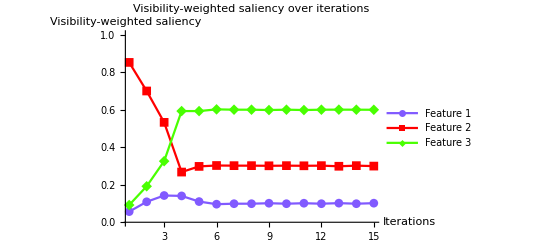

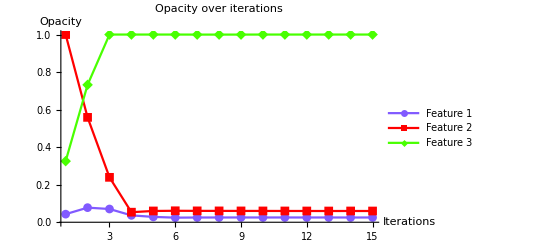

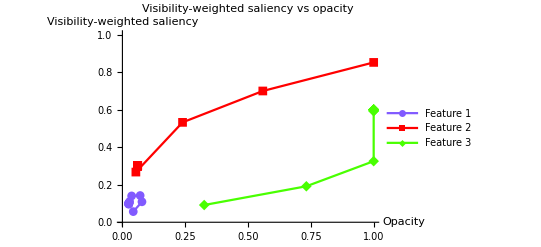

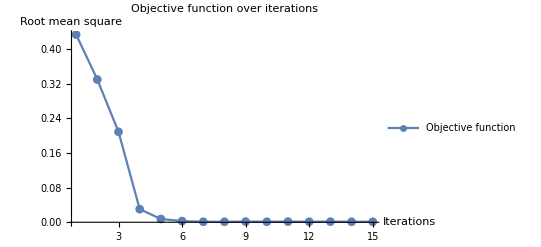

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.0566538
0.851543
0.0918031 | 0.0431373
1.
0.32549 | 0.433721 | 0.00433462
-0.0551543
0.0508197 | 8
2 | 0.109027
0.699312
0.191661 | 0.0778142
0.558766
0.732048 | 0.329784 | -0.000902684
-0.0399312
0.0408339 | 8
3 | 0.14244
0.532156
0.325404 | 0.0705927
0.239316
1. | 0.209046 | -0.00424397
-0.0232156
0.0274596 | 8
4 | 0.1403
0.267363
0.592337 | 0.0366409
0.053591
1. | 0.0302658 | -0.00403004
0.00326374
0.000766303 | 2
5 | 0.11017
0.297563
0.592268 | 0.0285809
0.0601185
1. | 0.00750894 | -0.00101697
0.000243727
0.00077324 | 4
6 | 0.0962455
0.302352
0.601402 | 0.024513
0.0610934
1. | 0.00268296 | 0.000375446
-0.000235199
-0.000140248 | 2
7 | 0.0988119
0.301527
0.599661 | 0.0252639
0.060623
0.99972 | 0.00113426 | 0.000118811
-0.000152739
0.0000339274 | 1
8 | 0.0988119
0.301527
0.599661 | 0.0253827
0.0604703
0.999753 | 0.00113426 | 0.000118811
-0.000152739
0.0000339274 | 1
9 | 0.10135
0.300759
0.597891 | 0.0255015
0.0603175
0.999787 | 0.00151034 | -0.00013496
-0.0000758946
0.000210854 | 1
10 | 0.0988185
0.301546
0.599635 | 0.0253665
0.0602416
0.999998 | 0.00114306 | 0.00011815
-0.000154621
0.0000364715 | 1
11 | 0.101356
0.300778
0.597866 | 0.0254847
0.060087
1. | 0.00152738 | -0.000135637
-0.0000777678
0.000213405 | 1
12 | 0.0988185
0.301546
0.599635 | 0.0253491
0.0600092
1. | 0.00114306 | 0.00011815
-0.000154621
0.0000364715 | 1
13 | 0.101768
0.298279
0.599953 | 0.0254672
0.0598546
1. | 0.00142497 | -0.000176815
0.000172137
4.67825×10^-6 | 1
14 | 0.0988185
0.301546
0.599635 | 0.0252904
0.0600268
1. | 0.00114306 | 0.00011815
-0.000154621
0.0000364715 | 1
15 | 0.101599
0.299164
0.599237 | 0.0254085
0.0598721
1. | 0.0011311 | -0.000159905
0.0000836078
0.0000762977 | 1

```mathematica
t2-t1
iteration
saliency3=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_linesearch.png",saliency3];
opacity3=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_linesearch.png",opacity3];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity3=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_linesearch.png",saliencyopacity3];
rmslist3=#3&@@@list;
rms3=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_linesearch.png",rms3];
table3=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_linesearch.png",table3];
path3=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path3]}];
```

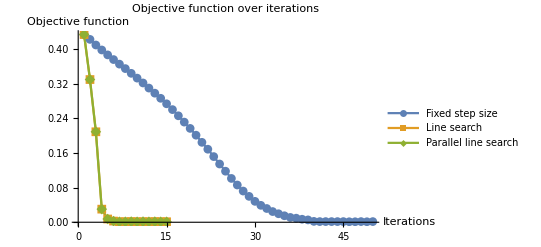

```mathematica
rmslists2=ListLinePlot[{rmslist1,rmslist2,rmslist3},PlotLegends->{"Fixed step size","Line search","Parallel line search"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Objective function"}]
Export[plotpath<>dataname<>"_rms_fixed_linesearch_parallel.png",rmslists2];
```

```mathematica
(*(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
iteration=0;
previous={0,{0,0,0},{0,0,0}};
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,gradient},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
gradient:=2*(mean-target);
(*steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,dy,dx},
{rms0,mean0,p0}=previous;
dy=Table[RootMeanSquare[Table[If[i==n,mean0[[i]],mean[[i]]],{i,Length[mean]}]-target],{n,Length[mean]}];
dx=peaks-p0;
If[Product[i,{i,dx}]≠0,-dy/dx*stepsize,-gradient*stepsize]
]];*)
steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,dy,dx},
{rms0,mean0,p0}=previous;
dy=mean-mean0;
dx=peaks-p0;
If[Product[i,{i,dx}]≠0,-dy/dx*gradient*stepsize,-gradient*stepsize]
]];
previous={rms,mean,peaks};
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps}
],{iterator,70}];*)
```

```mathematica
(*t2-t1
iteration
saliency4=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_difference.png",saliency4];
opacity4=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_difference.png",opacity4];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity4=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_difference.png",saliencyopacity4];
rms4=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_difference.png",rms4];
table4=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_difference.png",table4];
path4=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path4]}];*)
```

```mathematica
(*(* compare the performance of 3 methods for computing visibility-weighted saliency *)
n=10;

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ParallelMap[ImageMultiply[#,vis]&,{g1,g2}];
total=ParallelMap[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=ParallelTable[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ImageMultiply[g1,vis];(* weighted by lightness DoG (difference of Gaussians) *)
(*vs=Table[ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,features}];*)
total=ImageMeasurements[viss,"TotalIntensity"];
vs=ParallelTable[If[total≠0,ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/total,0],{i,features}];
viss2=ImageMultiply[g2,vis];(* weighted by chroma DoG *)
(*vs2=Table[ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,features}];*)
total2=ImageMeasurements[viss2,"TotalIntensity"];
vs2=ParallelTable[If[total2≠0,ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/total2,0],{i,features}];
mean=Mean[{vs,vs2}]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n*)
```

```mathematica
recordxml=plotpath<>"records.xml";
recordmap=If[FileExistsQ[recordxml],Association@Import[recordxml],<||>];
AssociateTo[recordmap,dataname->records];
Export[recordxml,Normal[recordmap]];
dataname->records
```

nucleon_strong_red→{{2.85338,37,{0.0253103,0.0602932,1.}},{2.845624,37,{0.0255004,0.0603797,1.}},{1.778634,4,{0.0252705,0.0601541,1.}},{1.246601,4,{0.0254085,0.0598721,1.}}}

```mathematica
ObjectiveFunction[pos_]:=RootMeanSquare[VisibilitySaliency[pos]-target];
```

```mathematica
(*ObjectiveFunction[{0.1,0.3,0.6}]
(*FindMinimum[{ObjectiveFunction[{x1,x2,x3}],0≤x1≤1,0≤x2≤1,0≤x3≤1},{{x1,{0.1}},{x2,{0.3}},{x3,{0.6}}}]*)
FindMinimum[x1 Cos[x1]+x2 Cos[x2],{{x1,0},{x2,0}}]
Plot3D[x1 Sin[x1]+x2 Sin[x2],{x1,0,10},{x2,0,10}]*)
```

```mathematica
(*range=Range[0,1,0.1];
coordinates=Flatten[Table[{i,j,k},{i,range},{j,range},{k,range}],2];
Length[coordinates]
AbsoluteTiming[
searchspace=ParallelTable[Module[{mean,rms},
mean=VisibilitySaliency[c];
rms=RootMeanSquare[mean-target];
{mean,c,rms}
],{c,coordinates}];
]*)
```

```mathematica
(*transform=RotationTransform[-90 Degree,{0,0,1}];
vec=transform[{1.3, -2.4, 2.}];
opacitylist=#2&@@@searchspace;
rmslist=#3&@@@searchspace;
merged=ParallelTable[Append[opacitylist[[i]],rmslist[[i]]],{i,Length[opacitylist]}];
densityplot=ListDensityPlot3D[merged,ColorFunction->"LightTemperatureMap",PlotLegends->Automatic,PlotLabel->{"x","y","z"},PlotTheme->"Detailed",OpacityFunction->Automatic];
paths={path1,path3};
pathcolors={Red,Green,Blue};
plotlegends={{"Fixed step size"},{"Adaptive step size with line search"},{"Adaptive step size with parallel search"}};
pointplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]],Thick,PointSize[Large]},PlotLegends->plotlegends[[i]]],{i,Length[paths]}];
lineplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]]}]/.Point->Line,{i,Length[paths]}];
sp=Show[densityplot,PlotLabel->"Objective function in parameter space",ViewPoint->vec]
sp2=Show[densityplot,pointplots[[1]],pointplots[[2]],lineplots[[1]],lineplots[[2]],PlotLabel->"Gradient descent in parameter space",ViewPoint->vec]
Export[plotpath<>dataname<>"_parameterspace.png",sp];
Export[plotpath<>dataname<>"_parameterspace_path.png",sp2];

{c1,c2,c3}=chartcolors;
blend1=Blend[{{0,Black},{0.5,c1},{1,White}},#]&;
blend2=Blend[{{0,Black},{0.5,c2},{1,White}},#]&;
blend3=Blend[{{0,Black},{0.5,c3},{1,White}},#]&;
saliencylist=#&@@@searchspace;
first=#&@@@saliencylist;
second=#2&@@@saliencylist;
third=#3&@@@saliencylist;
merged1=ParallelTable[Append[opacitylist[[i]],first[[i]]],{i,Length[opacitylist]}];
merged2=ParallelTable[Append[opacitylist[[i]],second[[i]]],{i,Length[opacitylist]}];
merged3=ParallelTable[Append[opacitylist[[i]],third[[i]]],{i,Length[opacitylist]}];
dplots=ListDensityPlot3D[#1,ColorFunction->#2,PlotLegends->Automatic,PlotTheme->"Detailed",OpacityFunction->(#&)]&@@@{{merged1,blend1},{merged2,blend2},{merged3,blend3}};
densityplots=MapIndexed[Show[#,PlotLabel->"Visibility-weighted saliency of feature "<>ToString[First@#2],ViewPoint->vec]&,dplots]
MapIndexed[Export[plotpath<>dataname<>"_densityplot"<>ToString[First@#2]<>".png",#]&,densityplots];*)
```

```mathematica
saveTransferFunction[peaks_,filename_]:=Module[{a2,rgba2,intensity2,rgbafunction2,rgba2denormalized,xrgba,strlist,alphaMode,gammaValue,domain,threshold,k,int,split,colorL,keylist,keys,TransFuncIntensity,VoreenData,xml},
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
a2=IntegerPart[255*alpha0[[#]]]&/@rangeOfAlpha;
rgba2=(#/255.&)/@Transpose[{r,g,b,a2}]//(RGBColor/@#&);
intensity2=intensity0[[#]]&/@rangeOfAlpha;
rgbafunction2=(Blend[Transpose[{intensity2,rgba2}], #] & );(* for return only. not used in this function *)

rgba2denormalized=Transpose[{r,g,b,a2}];
xrgba=Table[Join[{intensity2[[i]]},rgba2denormalized[[i]]],{i,Length[intensity2]}];
strlist={ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&@@@xrgba;
alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({int=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xml=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function exported from Mathematica"]},VoreenData,{}];
Export[filename,xml, "XML"];
rgbafunction2
];
```

```mathematica
tf1=saveTransferFunction[Last[path1],plotpath<>dataname<>"_optimized_fixed.tfi"];
tf2=saveTransferFunction[Last[path2],plotpath<>dataname<>"_optimized_parallelsearch.tfi"];
tf3=saveTransferFunction[Last[path3],plotpath<>dataname<>"_optimized_linesearch.tfi"];
Image3D[d,ColorFunction->rgbafunction,ViewPoint->viewpoints[face]]
Image3D[d,ColorFunction->tf3,ViewPoint->viewpoints[face]]
ListLinePlot[Transpose[{intensity,alpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"Before optimization"]
(*Transpose[{intensity,r,g,b,a}]*)
ListLinePlot[Transpose[{intensity0[[#]]&/@rangeOfAlpha,alpha0[[#]]&/@rangeOfAlpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"After optimization"]
(*xrgba*)
```

-Graphics-

-Graphics-